```mathematica
ClearAll["Global`*"];  (*Clear all variables*)

(*Initialize an empty list to store results*)
results={};

(*Loop over the parameter space*)
For[k12=1,k12<=5,k12+=1,
For[k21=1,k21<=5,k21+=1,
For[m1h=0.1,m1h<=0.2,m1h+=0.02,
For[m2h=0.1,m2h<=0.2,m2h+=0.02,

(*Update kMatrix and mortality rates*)
kMatrix={{5,k12},
	        {k21,5}};

parameters={DN1->0.5,DN2->0.7,DR1->2.2,DR2->2,K->1,m1->m1h,m2->m2h,L->30,N10->1,N20->1,TOTALTIME->100,n->2,Y1->2,Y2->1};

(* Solving the PDEs *)
(*Define g and f functions for each species i and resource j*)
g[i_,j_,R_,Y_]:=Y kMatrix[[i,j]] R;
	f[i_,j_,N_,R_]:=kMatrix[[i,j]] N R;

	(*Define the initial conditions with C1 and C2*)
	R1Init[x_,C1_]:=C1 (1-x/L)^n/. parameters;
	R2Init[x_,C2_]:=C2 (1-x/L)^n/. parameters;
	
(*Take the derivatives at x=0 and x=L*)
dR1Init0[C1_]=D[R1Init[x,C1],x]/. x->0;
	dR2Init0[C2_]=D[R2Init[x,C2],x]/. x->0;
	dR1InitL[C1_]=D[R1Init[x,C1],x]/. x->L/. parameters;
	dR2InitL[C2_]=D[R2Init[x,C2],x]/. x->L/. parameters;
	
(*Solve for C1 and C2 self-consistently*)
eq1=dR1Init0[C1]==K-f[1,1,N10,R1Init[0,C1]]-f[2,1,N20,R1Init[0,C1]]/. parameters;
	eq2=dR2Init0[C2]==K-f[1,2,N10,R2Init[0,C2]]-f[2,2,N20,R2Init[0,C2]]/. parameters;
	eq3=dR1InitL[C1]==0;
	eq4=dR2InitL[C2]==0;
	
sol=Solve[{eq1,eq2,eq3,eq4},{C1,C2}];
	C1sol=C1/. First[sol];
	C2sol=C2/. First[sol];

(*Define the PDE system*)
PDEs={
D[N1[t,x],t]==DN1 Laplacian[N1[t,x],{x}]+N1[t,x]*(g[1,1,R1[t,x],Y1]+g[1,2,R2[t,x],Y2]-m1),D[N2[t,x],t]==DN2 Laplacian[N2[t,x],{x}]+N2[t,x]*(g[2,1,R1[t,x],Y1]+g[2,2,R2[t,x],Y2]-m2),D[R1[t,x],t]==DR1 Laplacian[R1[t,x],{x}]-f[1,1,N1[t,x],R1[t,x]]-f[2,1,N2[t,x],R1[t,x]],D[R2[t,x],t]==DR2 Laplacian[R2[t,x],{x}]-f[1,2,N1[t,x],R2[t,x]]-f[2,2,N2[t,x],R2[t,x]]
}/. parameters;
	
(*Modified Neumann boundary conditions*)
bc={
Derivative[0,1][N1][t,0]==0,
Derivative[0,1][N1][t,L]==0,
Derivative[0,1][N2][t,0]==0,
Derivative[0,1][N2][t,L]==0,
Derivative[0,1][R1][t,0]==K-f[1,1,N1[t,0],R1[t,0]]-f[2,1,N2[t,0],R1[t,0]],Derivative[0,1][R1][t,L]==-f[1,1,N1[t,L],R1[t,L]]-f[2,1,N2[t,L],R1[t,L]],Derivative[0,1][R2][t,0]==K-f[1,2,N1[t,0],R2[t,0]]-f[2,2,N2[t,0],R2[t,0]],
Derivative[0,1][R2][t,L]==-f[1,2,N1[t,L],R2[t,L]]-f[2,2,N2[t,L],R2[t,L]]
}/. parameters;
	
(*Initial conditions with solved C1sol and C2sol*)
ic={N1[0,x]==N10/. parameters,N2[0,x]==N20/. parameters,R1[0,x]==C1sol (1-x/L)^n/. parameters,R2[0,x]==C2sol (1-x/L)^n/. parameters};
	
(*Solve the PDE system numerically*)
solution=NDSolve[Join[PDEs,bc,ic],{N1,N2,R1,R2},{t,0,TOTALTIME/. parameters},{x,0,L/. parameters}];

(*Make sure the PDEs are solved before proceeding*)If[Head[solution]===NDSolve,Print["Failed to solve PDEs for parameters: ",{k12,k21,m1h,m2h}];
Continue[]];

(*Calculate the fraction of N1 at t=TOTALTIME*)
totalN1=NIntegrate[N1[TOTALTIME,x]/.parameters/. First[solution],{x,0,L/. parameters}];
totalN2=NIntegrate[N2[TOTALTIME,x]/.parameters/. First[solution],{x,0,L/. parameters}];
fractionN1=totalN1/(totalN1+totalN2);

(*Store the result*)
AppendTo[results,{k12/k21,m1h/m2h,fractionN1}];
]
]
]
]
```

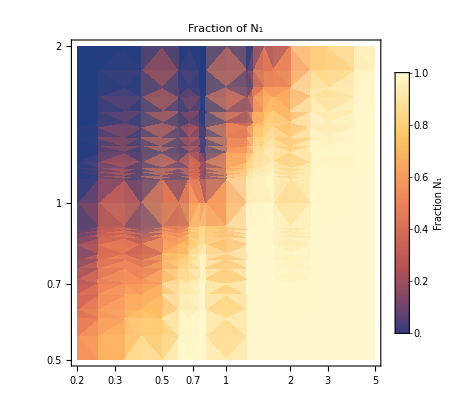
-Graphics-m_1/m_2k_12/k_21

```mathematica
(*Generate the heatmap*)
Labeled[ListDensityPlot[results,PlotLegends->BarLegend[Automatic,LegendLabel->Rotate["Fraction N_1",90Degree]],PlotLabel->"Fraction of N_1",ScalingFunctions->{"Log","Log"}],{Rotate["m_1/m_2",90 Degree],"k_12/k_21"},{Left,Bottom}]
```